# UniDyn--Demo-03.nb

John A. Marohn
jam99@cornell.edu
Cornell University

Abstract:  This notebook demonstrates how to take the digital Fourier transform (DFT) of data.

## Introductory example illustrating one-dimensional DFT data ordering

Transverse magnetization, detected off resonance, decaying due to T2.  “Spike” the data with a dc offset (an ocscillation at zero frequency).  Make the dc offset large enough so we can see it but small enough so that it is not the largest peak in the spectrum.

```mathematica
Clear[y];
y[t_] := Cos[2 π (5.1) t] Exp[-t/2] + 0.075
```

To plot, set the total number of points (NN) and the total time (T).  We set NN equal to a power of 2 in anticipation of taking a digital Fourier transform.

```mathematica
NN = 2^10;
T = 10.0;
```

From NN and T we derive the time step (dt) and the frequency step (df).  Now generate a list of data points based on the above function.  At the same time, generate a list of time points (t) and frequency points (f) for plotting.

```mathematica
dt = T/(NN-1);
df = 1/dt;

Y = Table[y[t],{t,0,T,dt}];

f = Table[jj/T,{jj,-NN/2,NN/2-1}];
t = Table[ii*dt,{ii,0,NN-1}];

Print["The time step is ",dt," s"]
Print["The Nyquist frequency is ",1/(2*dt)," Hz"]
```

The time step is 0.00977517 s

The Nyquist frequency is 51.15 Hz

Plot the data versus time:

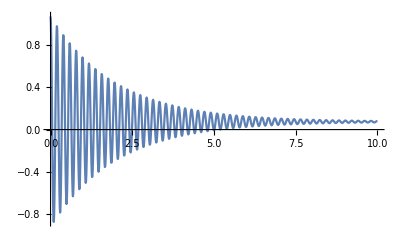

```mathematica
ListLinePlot[Transpose[{t,Y}],PlotRange-> All]
```

Take the Fourier transform and plot the absolute value of the Fourier transform.

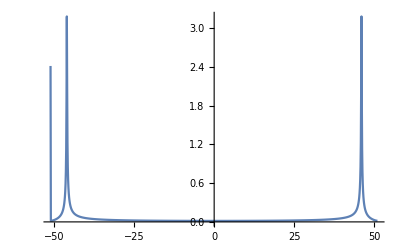

```mathematica
ListLinePlot[Transpose[{f,Abs[Fourier[Y]]}],PlotRange->All]
```

Note that we do not see peaks in the frequency spectrum where we expect.  This is because the DFT algorithm returns the data in a funny order -- positive-frequency data first, then negative-frequency data.  If we want the DFT’ed data running from negative frequency to positive frequency, then we need to reorder the data.  Below we accomplish this reordering with the RotateLeft[] function.

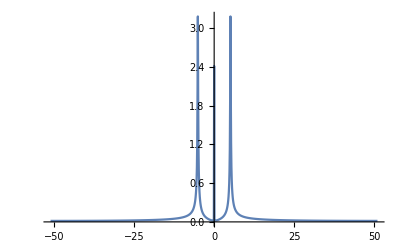

```mathematica
FFTY = RotateRight[Fourier[Y],NN/2];
ListLinePlot[Transpose[{f,Abs[FFTY]}],PlotRange->All]
```

Now the plot looks right.  Check that there is a peak at zero frequency due to the dc offest.  Do this by printing out the data near the middle of the spectrum:

```mathematica
{f[[#]],Abs[FFTY][[#]]}& /@  {NN/2}
{f[[#]],Abs[FFTY][[#]]}& /@  {NN/2+1}
{f[[#]],Abs[FFTY][[#]]}& /@  {NN/2+2}
```

{{-0.1,0.017401}}

{{0.,2.41729}}

{{0.1,0.017401}}

We can zoom in on the spectrum near zero frequency:

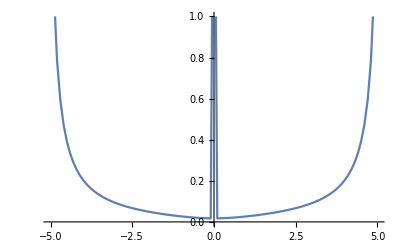

```mathematica
ListLinePlot[Transpose[{f,Abs[FFTY]}],PlotRange->{{-5,5},{0,1}}]
```

Print out the frequency of the peak in the absolute value of the Fourier Transform.  We see that the peak occurs at the expected frequency.

```mathematica
f[[Ordering[Abs[FFTY]][[-1]]]]
```

5.1

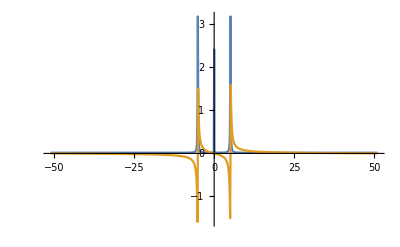

```mathematica
ListLinePlot[{Transpose[{f,Re[FFTY]}],Transpose[{f,Im[FFTY]}]},PlotRange-> All]
```

## Define our own one-dimensional DFT module and illustrate aliasing

This digital Fourier transform module, DFFT[], takes inputs

	y = the signal, versus time t
	NN = number of data points to plot (ideally a multiple of 2)
	T = the total length of time in seconds
	
and produces a plot of (1) the signal versus time and the (2) absolute value of DFT{signal} versus frequency.

```mathematica
DFFT[y_,NN_,T_] :=
Module[{dt,df,Y,f,t},

dt = T/(NN-1);
df = 1/dt;

Y = Table[y[t],{t,0,T,dt}];

f = Table[jj/T,{jj,-NN/2,NN/2-1}];
t = Table[ii*dt,{ii,0,NN-1}];

FFTY = RotateRight[Fourier[Y],NN/2];

p1= ListLinePlot[Transpose[{t,Y}],
PlotRange->{-1,1},
AxesLabel-> {"time [s]","signal"}];

p2=ListLinePlot[{Transpose[{f,Re[FFTY]}],Transpose[{f,Im[FFTY]}]},
PlotRange-> All,
AxesLabel->{"freq [Hz]","DFT{signal}"}];

Show[GraphicsGrid[{{p1,p2}}]]
]
```

Test drive the module

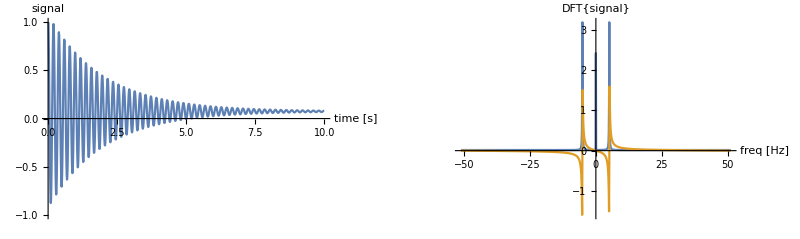

```mathematica
Clear[y];
y[t_] := Cos[2 π (5.1) t] Exp[-0.5 t] + 0.075
DFFT[y,2^10,10.]
```

Make an interactive graphic where we can vary the freqency and decay time of the oscillation while watching the signal oscillation versus time and the Fourier transform of the signal versus frequency.  This animation illustrates the problem of folding in or aliasing.

```mathematica
Manipulate[z[t_] := Cos[2 π f0 t] Exp[-t/τ]; DFFT[ z,2^10,10.],{f0,1,100},{τ,0.05,20}]
```

## Apodization and Zero Filling

When the data abruptly stops ... you get “sinc” wiggles

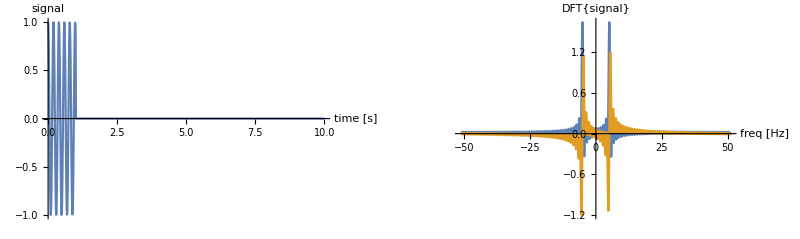

```mathematica
Clear[y];
y[t_] := Cos[2 π (5.1) t] /; t <= 1
y[t_] := 0 /; t > 1
DFFT[y,2^10,10.]
```

If, on the other hand, you force the data to decay ... then the sinc() wiggles largely go away.

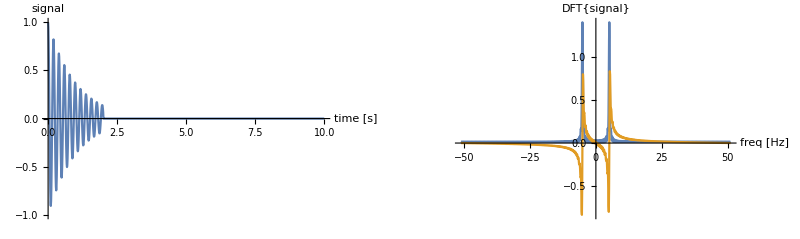

```mathematica
Clear[y];
y[t_] := Cos[2 π (5.1) t] Exp[-t/1]/; t <= 2
y[t_] := 0 /; t > 2
DFFT[y,2^10,10.]
```

The Exp[] function is not exactly zero at the cutoff time of 1 second in the above example, so some sinc() wiggles remain.  Are there better windows?  A Hanning window forces the data to zero at the end.

3.

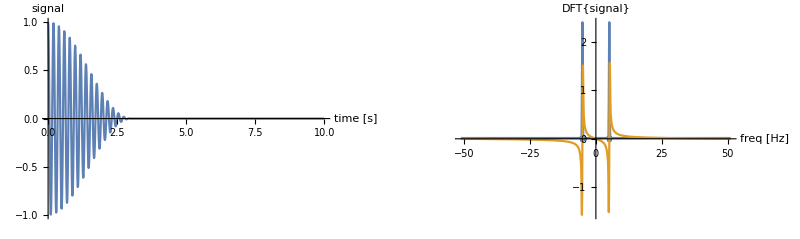

```mathematica
Clear[y];
T$cut = 3.0
y[t_] := Cos[2 π (5.1) t] 0.5(1+Cos[π t /T$cut])/; t <= T$cut
y[t_] := 0 /; t > T$cut
DFFT[y,2^10,10.]
```

Procedure:

 (1) Force data to zero with “apodization”
 (2) Extend the data with zeros until the length of the data is a power of 2
 (3) THEN Fourier transform

## Two-dimensional DFT

```mathematica
z[t1_,t2_] := Cos[2 π (2.1) t1] Exp[-t1/5] Cos[2 π (2.1) t2] Exp[-t2/5]+0.010
```

```mathematica
NN = 2^7;
T = 10.0;

dt = T/(NN-1);
df = 1/dt;
S = Table[z[t1,t2],{t1,0,T,dt},{t2,0,T,dt}];

Print["The timestep is ",dt," s"]
Print["The Nyquist frequency is ",1/(2*dt)," Hz"]
```

The timestep is 0.0787402 s

The Nyquist frequency is 6.35 Hz

```mathematica
ListPlot3D[S,PlotRange-> All]
```

-Graphics3D-

```mathematica
FFTS = RotateRight[Fourier[S],{NN/2,NN/2}];
ListPlot3D[Re[FFTS],PlotRange-> All]
```

-Graphics3D-

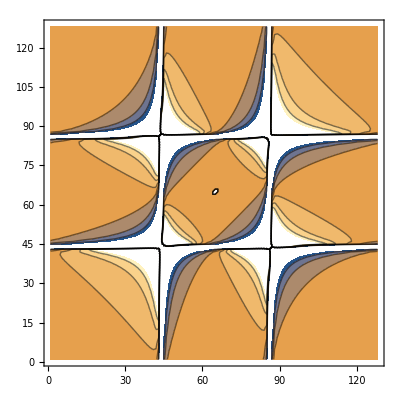

```mathematica
ListContourPlot[-Re[FFTS]]
```

### 2D DFT module (phase-twist lineshape)

```mathematica
D2DFFT[z_,NN_,T_] :=
Module[{dt,df,S,f,t},

dt = T/(NN-1);
df = 1/dt;

S = Table[z[t1,t2],{t1,0,T,dt},{t2,0,T,dt}];

f = Table[jj/T,{jj,-NN/2,NN/2-1}];
t = Table[ii*dt,{ii,0,NN-1}];

Print["The time step is ",dt," s"];
Print["The Nyquist frequency is ",1/(2*dt)," Hz"];

FFTS = RotateRight[Fourier[S],{NN/2,NN/2}];

SetOptions[ListPlot3D,PlotRange->All,PlotLabel->"",
DataRange->{{f[[1]],f[[-1]]},{f[[1]],f[[-1]]}}];

ListPlot3D[Re[FFTS],PlotRange-> All,
AxesLabel->{"f1 [Hz]","f2 [Hz]","2D DFT{signal}"}]

]
```

An example of the phase-twist lineshape

```mathematica
z[t1_,t2_] := Cos[2 π (2.1) t1] Exp[-t1/2] Cos[2 π (2.1) t2] Exp[-t2/2]+0.010
D2DFFT[z,2^8,10.]
```

The time step is 0.0392157 s

The Nyquist frequency is 12.75 Hz

-Graphics3D-

### 2D DFT module (pure absorption lineshape)

We obtain a pure absorbtion lineshape by Fourier transforming along one dimension, taking the real part, Fourier transforming along the other dimension, and taking the real part.  Stepwise, the procedure is:

	Cos[w1 t1] Exp[-k1 t1] Cos[w2 t2] Exp[-k2 t2]
	Cos[w1 t1] Exp[-k1 t1] (A[w2]+I D[w2])
	Cos[w1 t1] Exp[-k1 t1] A[w2]
	(A[w1] + I D[w2]) A[w2]
	A[w1] A[w2]
	
where we can see we end up with a pure abs lineshape at the end.  Implimenting the FT along just one dimension in Mathematica is a pain -- I have to resort to looping over each row/column and doing a 1D Fourier transform .... very inelegant.

```mathematica
D2DFFTabs[z_,NN_,T_] :=
Module[{dt,df,f,S,t},

dt = T/(NN-1);
df = 1/dt;

S = Table[z[t1,t2],{t1,0,T,dt},{t2,0,T,dt}];

f = Table[jj/T,{jj,-NN/2,NN/2-1}];
t = Table[ii*dt,{ii,0,NN-1}];

Print["The time step is ",dt," s"];
Print["The Nyquist frequency is ",1/(2*dt)," Hz"];

Sr = S;
Srr = S;

Do[Sr[[ii]]=Re[Fourier[S[[ii]]]],{ii,1,Dimensions[f][[1]]}];
Do[Srr[[ii]] = Re[Fourier[Transpose[Sr][[ii]]]],{ii,1,Dimensions[f][[1]]}];

FFTS = RotateRight[Transpose[Srr],{NN/2,NN/2}];

SetOptions[ListPlot3D,PlotRange->All,PlotLabel->"",
DataRange->{{f[[1]],f[[-1]]},{f[[1]],f[[-1]]}}];

p1=ListPlot3D[Re[FFTS],PlotRange-> All,
AxesLabel->{"f1 [Hz]","f2 [Hz]","2D DFT{signal}"}];

p2 = ListContourPlot[-Re[FFTS],PlotRange-> All,
AxesLabel->{"f1 [Hz]","f2 [Hz]"}];

Show[GraphicsGrid[Transpose[{{p1,p2}}]]]
]
```

An example of a pure-absorbtion lineshape

The time step is 0.0787402 s

The Nyquist frequency is 6.35 Hz

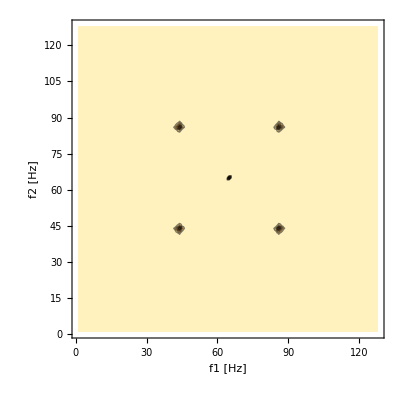

```mathematica
z[t1_,t2_] := Cos[2 π (2.1) t1] Exp[-t1/2] Cos[2 π (2.1) t2] Exp[-t2/2]+0.010
D2DFFTabs[z,2^7,10.]
```